```mathematica
Exit[];
```

```mathematica
c={1-3 n^2 x^2+2 n^3 x^3,3 n^2 x^2-2 n^3 x^3,x-2 n x^2+n^2 x^3,-n x^2+n^2 x^3}
```

{1-3 n^2 x^2+2 n^3 x^3,3 n^2 x^2-2 n^3 x^3,x-2 n x^2+n^2 x^3,-n x^2+n^2 x^3}

```mathematica
b=1/n;
```

```mathematica
Y[i_,h_]:={y[i],y[i+1],m[i],m[i+1]}.c/.x->h;
{Y[i,0],Y[i,1/n],D[Y[i,x],x]/.x->0,D[Y[i,x],x]/.x->1/n}
```

{y[i],y[1+i],m[i],m[1+i]}

```mathematica
Simplify[(D[Y[1,x],{x,2}]/4 /n/.x->0)==0]
```

2 m[1]+m[2]+3 n y[1]==3 n y[2]

```mathematica
Simplify[(D[Y[n,x],{x,2}]/4 /n/.x->b)==0]
```

m[n]+2 m[1+n]+3 n y[n]==3 n y[1+n]

```mathematica
Simplify[(D[Y[i,x],{x,2}]/4 /n/.x->b)==(D[Y[i+1,x],{x,2}]/4 /n/.x->0)]
```

m[i]+4 m[1+i]+m[2+i]+3 n y[i]==3 n y[2+i]

```mathematica
M[n_]:=SparseArray[{{1,1}->-2,(n+1){1,1}->2,{n+1,n}->-2,{1,2}->2,{i_,j_}/;(i==j+1&&i<n+1&&i>1)->-1,{i_,j_}/;(i==j-1&&i<n+1&&i>1)->1},(n+1){1,1}];
M[5]//MatrixForm
```

(-2 | 2 | 0 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0 | 0
0 | -1 | 0 | 1 | 0 | 0
0 | 0 | -1 | 0 | 1 | 0
0 | 0 | 0 | -1 | 0 | 1
0 | 0 | 0 | 0 | -2 | 2)

# los:

```mathematica
y={1,2,4,5,10,1,2,3,4,1};m=M[Length[y]-1].y;n=Length[y]-1;
```

```mathematica
Y[x0_]:=Module[{i,x=x0,y=y,m=m,c=c,n=n},
i=Ceiling[x*n];
x-=(i-1)/n;
{y[[i]],y[[i+1]],m[[i]],m[[i+1]]}.{1-3 n^2 x^2+2 n^3 x^3,3 n^2 x^2-2 n^3 x^3,x-2 n x^2+n^2 x^3,-n x^2+n^2 x^3}
]
```

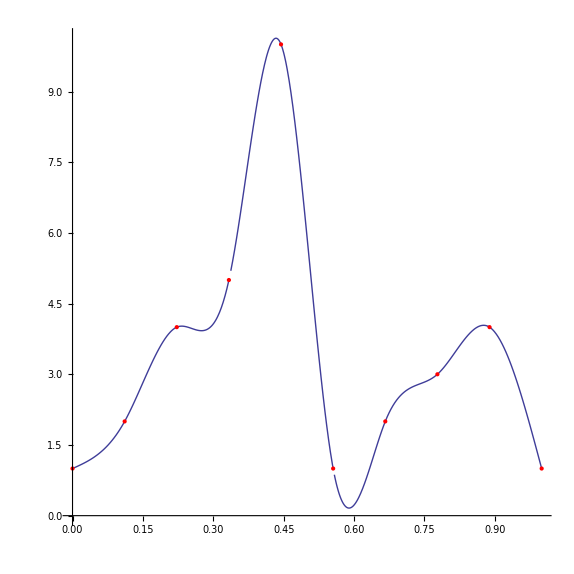

```mathematica
Show[Plot[Y[x],{x,0,1},AspectRatio->1,PlotPoints->250],ListPlot[Table[{i/(Length[y]-1),y[[i+1]]},{i,0,Length[y]-1}],PlotStyle->Red]]
```

```mathematica
<<Splines`
```

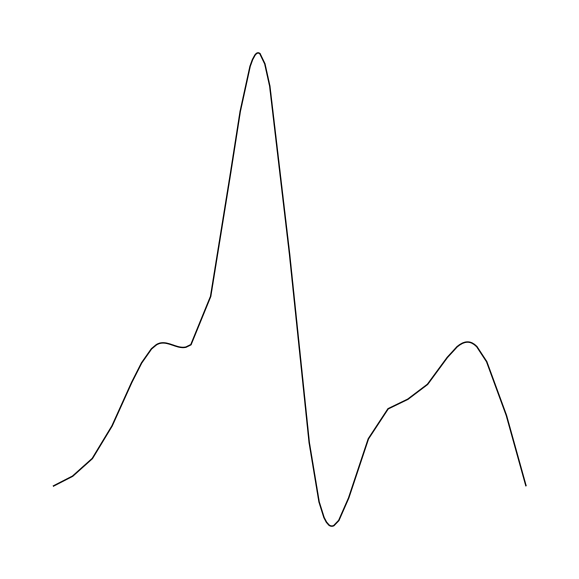

```mathematica
Graphics[Spline[Table[{i/(Length[y]-1),y[[i+1]]},{i,0,Length[y]-1}],Cubic],AspectRatio->1]
```

```mathematica
Y[x0_]:=Module[{i=n,x=x0,p=P,m=m,kr=kr,n=n,b,y},
If[x0==0,i=1,
While[x≤p[[i,1]],i--];
];
b=p[[i+1,1]]-p[[i,1]];
{p[[i,2]],p[[i+1,2]],m[[i]],m[[i+1]],kr[[i,1]],kr[[i,2]]}.{1-(10 y^3)/b^3+(15 y^4)/b^4-(6 y^5)/b^5,(10 y^3)/b^3-(15 y^4)/b^4+(6 y^5)/b^5,y-(6 y^3)/b^2+(8 y^4)/b^3-(3 y^5)/b^4,-(4 y^3)/b^2+(7 y^4)/b^3-(3 y^5)/b^4,y^2/2-(3 y^3)/(2 b)+(3 y^4)/(2 b^2)-y^5/(2 b^3),y^3/(2 b)-y^4/b^2+y^5/(2 b^3)}/.y->(x-p[[i,1]])
]
```

```mathematica
n=20;nN=Length[XY];
P=Join[{1},Table[i,{i,Ceiling[(nN-(Floor[nN/n]-1)n)/2],nN,n}],{nN}];
n=Length[P]-1;
P=Table[{XY[[P[[i]],1]],XY[[P[[i]],2]]},{i,1,n+1}]
tt=Table[ts[i],{i,3*n+1}];
m=tt[[1;;n+1]];kr=Transpose[{tt[[n+2;;2 n+1]],tt[[2 n+2;;3n+1]]}];
```

{{0,-0.011473},{0.161017,-0.000802},{0.330508,-0.000373},{0.5,0.000026},{0.669492,0.00068},{0.838983,0.001158},{1.,0.011826}}

```mathematica
d=(Y[#[[1]]]-#[[2]])^2&/@XY;d=Sum[d[[i]],{i,Length[d]}];g=Solve[Table[D[d,ts[i]]==0,{i,3*n+3}],tt]
```

{{ts[1]→0.732286,ts[2]→0.0432745,ts[3]→0.0155775,ts[4]→0.00826988,ts[5]→0.0258178,ts[6]→0.0717768,ts[7]→0.91313,ts[8]→-39.1332,ts[9]→-3.55332,ts[10]→-1.18621,ts[11]→-0.690975,ts[12]→-3.15685,ts[13]→-12.2057,ts[14]→7.49265,ts[15]→1.63073,ts[16]→0.59971,ts[17]→1.85439,ts[18]→6.06894,ts[19]→53.9935}}

```mathematica
tt=Table[ts[i],{i,3*n+1}]/.g[[1]];
```

```mathematica
d/.g[[1]]
```

0.0000251891

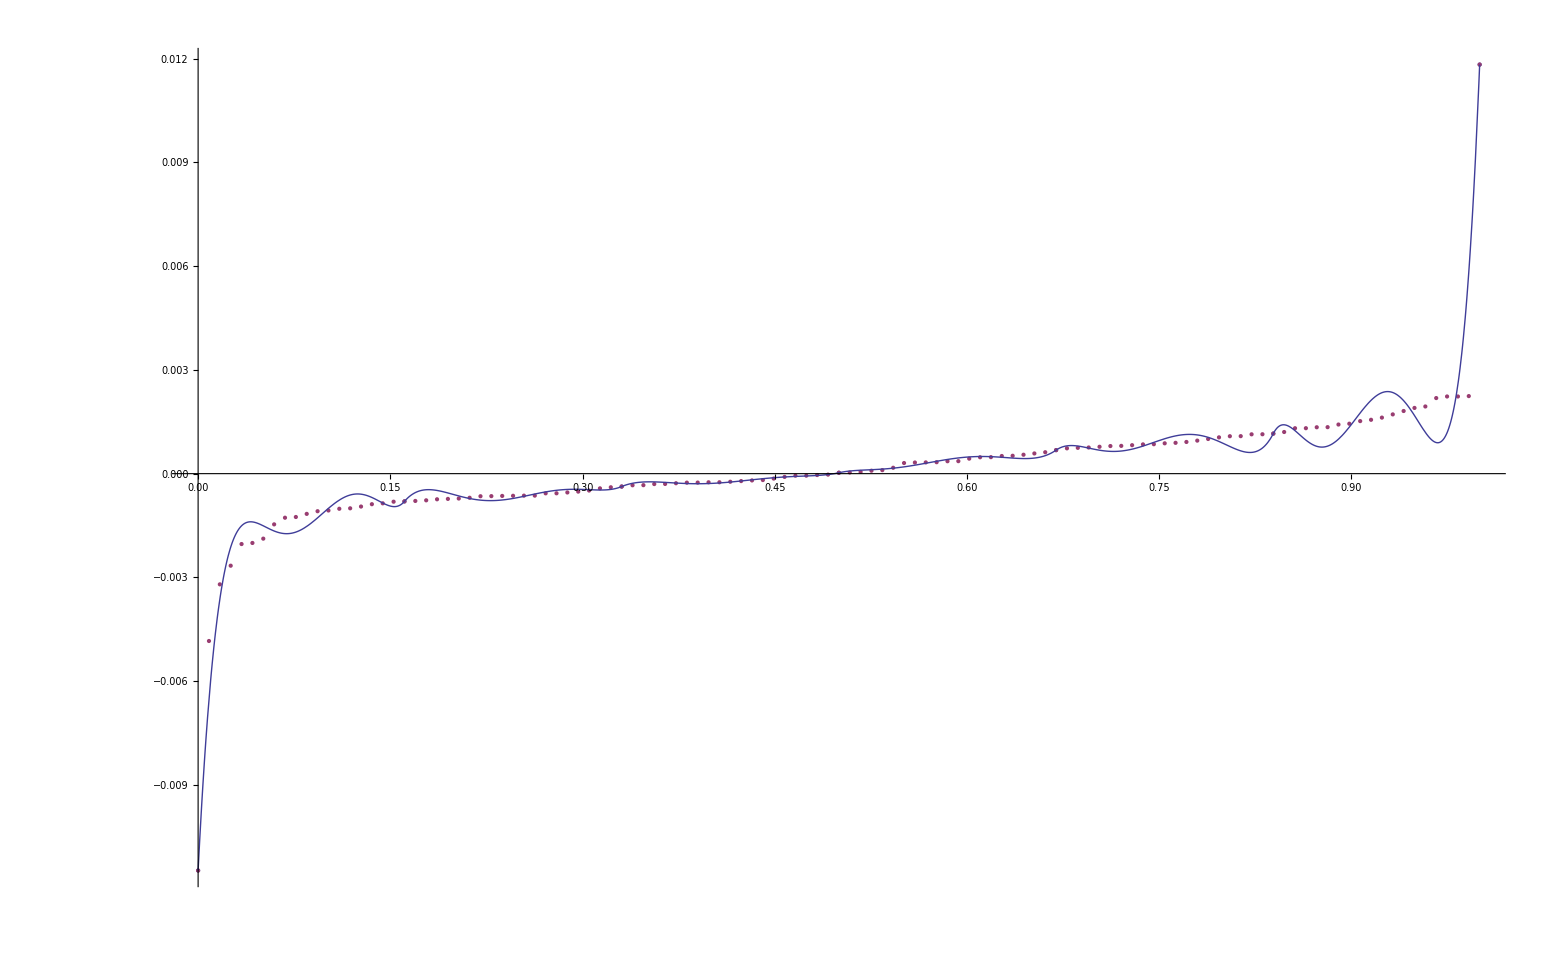

```mathematica
Show[ListPlot[{P,XY},PlotRange->All],Plot[Y[x]/.g[[1]],{x,0,1},PlotRange->All]]
```

```mathematica
Solve[Table[D[d,ys[i]]==0,{i,nN}],Table[ys[i],{i,nN}]]
```

{{ys[1]→-0.00547464,ys[2]→-0.000492335,ys[3]→-0.000911088,ys[4]→-0.00031071,ys[5]→-0.000185091,ys[6]→0.000265952,ys[7]→0.00060474,ys[8]→0.00113058,ys[9]→0.00100276,ys[10]→0.0046597}}

```mathematica
y=Table[ys[i],{i, nN}]/.%[[1]];
```

```mathematica
nN=10;y=Table[ys[i],{i, nN}];
```

0.000118941

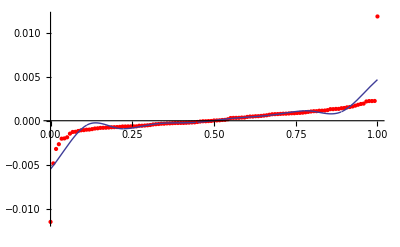

```mathematica
m=n/2M[n].y;n=Length[y]-1;d=(Y[#[[1]]]-#[[2]])^2&/@XY;d=Sum[d[[i]],{i,Length[d]}]
Show[ListPlot[XY,PlotStyle->Red,PlotRange->All],Plot[Y[x],{x,0,1},PlotRange->All]]
```

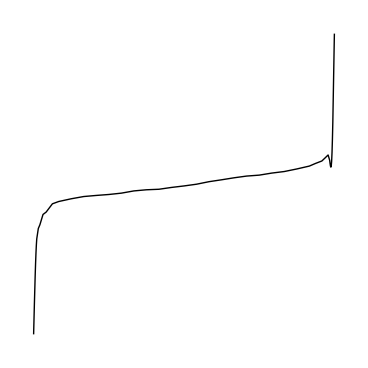

```mathematica
Graphics[Spline[XY,Cubic],AspectRatio->1]
```

```mathematica
Y[0]
```

0.01

```mathematica
{#[[1]]}&/@XY
```

{{0.},{0.008475},{0.016949},{0.025424},{0.033898},{0.042373},{0.050847},{0.059322},{0.067797},{0.076271},{0.084746},{0.09322},{0.101695},{0.110169},{0.118644},{0.127119},{0.135593},{0.144068},{0.152542},{0.161017},{0.169492},{0.177966},{0.186441},{0.194915},{0.20339},{0.211864},{0.220339},{0.228814},{0.237288},{0.245763},{0.254237},{0.262712},{0.271186},{0.279661},{0.288136},{0.29661},{0.305085},{0.313559},{0.322034},{0.330508},{0.338983},{0.347458},{0.355932},{0.364407},{0.372881},{0.381356},{0.389831},{0.398305},{0.40678},{0.415254},{0.423729},{0.432203},{0.440678},{0.449153},{0.457627},{0.466102},{0.474576},{0.483051},{0.491525},{0.5},{0.508475},{0.516949},{0.525424},{0.533898},{0.542373},{0.550847},{0.559322},{0.567797},{0.576271},{0.584746},{0.59322},{0.601695},{0.610169},{0.618644},{0.627119},{0.635593},{0.644068},{0.652542},{0.661017},{0.669492},{0.677966},{0.686441},{0.694915},{0.70339},{0.711864},{0.720339},{0.728814},{0.737288},{0.745763},{0.754237},{0.762712},{0.771186},{0.779661},{0.788136},{0.79661},{0.805085},{0.813559},{0.822034},{0.830508},{0.838983},{0.847458},{0.855932},{0.864407},{0.872881},{0.881356},{0.889831},{0.898305},{0.90678},{0.915254},{0.923729},{0.932203},{0.940678},{0.949153},{0.957627},{0.966102},{0.974576},{0.983051},{0.991525},{1.}}